# Scattering Kernels in 3D

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Binomial Scattering

```mathematica
pBinomial[u_,n_]:=Pi^-1((n+1)/2^(n+2))(1+u)^n
```

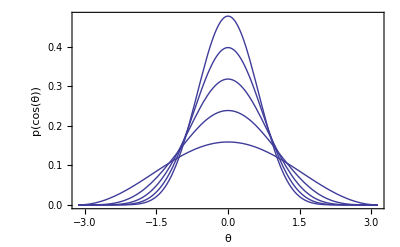

```mathematica
pBinplot=Show[
Plot[pBinomial[Cos[t],1],{t,-Pi,Pi},PlotRange->All],
Plot[pBinomial[Cos[t],2],{t,-Pi,Pi},PlotRange->All],
Plot[pBinomial[Cos[t],3],{t,-Pi,Pi},PlotRange->All],
Plot[pBinomial[Cos[t],4],{t,-Pi,Pi},PlotRange->All],
Plot[pBinomial[Cos[t],5],{t,-Pi,Pi},PlotRange->All],
Frame->True,
ImageSize->400,
FrameLabel->{{p[Cos[θ]],},{θ,"Binomial Scattering, n = 1, 2, 3, 4, 5"}}]
```

### Normalization condition

```mathematica
Integrate[2 Pi pBinomial[u,n],{u,-1,1},Assumptions->n≥0]
```

1

### Mean cosine (g)

```mathematica
Integrate[2 Pi pBinomial[u,n]u,{u,-1,1},Assumptions->n≥0]
```

n/(2+n)

### sampling

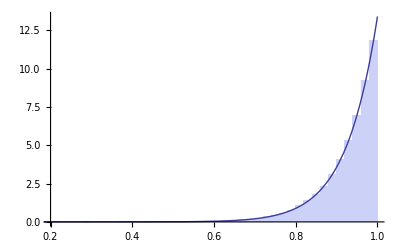

```mathematica
n=25.8;
Show[Histogram[Map[-1+(2^(1+n) #)^(1/(1+n))&,Table[RandomReal[],{i,1,100000}]],50,"PDF"],
Plot[2 Pi pBinomial[u,n],{u,-1,1},PlotRange->All]

]
Clear[b];
```

```mathematica
Integrate[2Pi(2k+1)pBinomial[u,n]LegendreP[k,u]/.k->0,{u,-1,1},Assumptions->n>1]
```

1

```mathematica
Integrate[2Pi(2k+1)pBinomial[u,n]LegendreP[k,u]/.k->1,{u,-1,1},Assumptions->n>1]
```

(3 n)/(2+n)

```mathematica
Integrate[2Pi(2k+1)pBinomial[u,n]LegendreP[k,u]/.k->2,{u,-1,1},Assumptions->n>1]
```

(5 (-1+n) n)/(6+5 n+n^2)

```mathematica
Integrate[2Pi(2k+1)pBinomial[u,n]LegendreP[k,u]/.k->3,{u,-1,1},Assumptions->n>1]
```

(7 (-2+n) (-1+n) n)/((2+n) (3+n) (4+n))

```mathematica
Integrate[2Pi(2k+1)pBinomial[u,n]LegendreP[k,u]/.k->4,{u,-1,1},Assumptions->n>1]
```

(9 (-3+n) (-2+n) (-1+n) n)/((2+n) (3+n) (4+n) (5+n))

```mathematica
Integrate[2Pi(2k+1)pBinomial[u,n]LegendreP[k,u]/.k->11,{u,-1,1},Assumptions->n>1]/(((1+2 j) Gamma[2+n])/(Gamma[1-j+n] Pochhammer[1+n,1+j])/.j->11)//FullSimplify
```

1